# Modèle 1.5 : Parasitoïde d’oeufs αl = 0

## Présentation du modèle

```mathematica
ModeleComplet= {
U'[t] == q A[t] -a U[t]P[t]- δu U[t]- q A[t-τu] Hp[t],
L'[t] == q A[t-τu] Hp[t] -δl L[t] - q A[t-τu-τl]Hp[t-τl] Exp[-τl δl],
M'[t] == q A[t-τu-τl]Hp[t-τl] Exp[-τl δl] - δm M[t] - q A[t-τu-τl-τm] Hp[t-τl-τm]Exp[-τl δl]Exp[-δm τm],
A'[t] == q A[t-τu-τl-τm] Hp[t-τl-τm]Exp[-τl δl]Exp[-δm τm] -δa A[t],
J'[t] ==a U[t]P[t]-δj J[t]-a U[t-τj]P[t-τj] Exp[-δj τj],
P'[t] ==a U[t-τj]P[t-τj] Exp[-δj τj]-δp P[t],
Hp'[t] ==-a Hp[t](P[t]-P[t-τu])
}
ModeleReduit = {
U'[t] == q A[t] -a U[t]P[t]- δu U[t]- q A[t-τu] Hp[t],
A'[t] == q A[t-τu-τl-τm] Hp[t-τl-τm]Exp[-τl δl]Exp[-δm τm] -δa A[t],
P'[t] ==a U[t-τj]P[t-τj] Exp[-δj τj]-δp P[t],
Hp'[t] ==-a Hp[t](P[t]-P[t-τu])
}
ModeleQuentin = {
U'[t] == q A[t] -a U[t]P[t]- δu U[t]- q A[t-τu] Exp[Hp[t]],
A'[t] == q A[t-τu-τl-τm] Exp[Hp[t-τl-τm]]Exp[-τl δl]Exp[-δm τm] -δa A[t],
P'[t] ==a U[t-τj]P[t-τj] Exp[-δj τj]-δp P[t],
Hp'[t] ==-a (P[t]-P[t-τu])
}
```

{U'[t]==q A[t]-q A[t-τu] Hp[t]-δu U[t]-a P[t] U[t],L'[t]==q A[t-τu] Hp[t]-ⅇ^(-δl τl) q A[t-τl-τu] Hp[t-τl]-δl L[t],M'[t]==ⅇ^(-δl τl) q A[t-τl-τu] Hp[t-τl]-ⅇ^(-δl τl-δm τm) q A[t-τl-τm-τu] Hp[t-τl-τm]-δm M[t],A'[t]==-δa A[t]+ⅇ^(-δl τl-δm τm) q A[t-τl-τm-τu] Hp[t-τl-τm],J'[t]==-δj J[t]+a P[t] U[t]-a ⅇ^(-δj τj) P[t-τj] U[t-τj],P'[t]==-δp P[t]+a ⅇ^(-δj τj) P[t-τj] U[t-τj],Hp'[t]==-a Hp[t] (P[t]-P[t-τu])}

{U'[t]==q A[t]-q A[t-τu] Hp[t]-δu U[t]-a P[t] U[t],A'[t]==-δa A[t]+ⅇ^(-δl τl-δm τm) q A[t-τl-τm-τu] Hp[t-τl-τm],P'[t]==-δp P[t]+a ⅇ^(-δj τj) P[t-τj] U[t-τj],Hp'[t]==-a Hp[t] (P[t]-P[t-τu])}

{U'[t]==q A[t]-ⅇ^Hp[t] q A[t-τu]-δu U[t]-a P[t] U[t],A'[t]==-δa A[t]+ⅇ^(-δl τl-δm τm+Hp[t-τl-τm]) q A[t-τl-τm-τu],P'[t]==-δp P[t]+a ⅇ^(-δj τj) P[t-τj] U[t-τj],Hp'[t]==-a (P[t]-P[t-τu])}

## Étude analytique

## Points fixes

### Valeur à l’équilibre des taux de mortalité non fixe

```mathematica
HpEqNnTri = Exp[-τu(δu+a Peq)];
```

### Modèle à l’équilibre

```mathematica
ModeleEq = {
0 == q Aeq -a Ueq Peq- δu Ueq- q Aeq Hpeq,
0 == q Aeq Hpeq Exp[-τl δl]Exp[-δm τm] -δa Aeq,
0 ==a Ueq Peq Exp[-δj τj]-δp Peq
};
MatrixForm[ModeleEq /.{Hpeq->HpEqNnTri}]
```

(0==Aeq q-Aeq ⅇ^(-((a Peq+δu) τu)) q-a Peq Ueq-Ueq δu
0==Aeq ⅇ^(-δl τl-δm τm-(a Peq+δu) τu) q-Aeq δa
0==a ⅇ^(-δj τj) Peq Ueq-Peq δp)

### Résolution globale

```mathematica
SolGen = Solve[ModeleEq /.{Hpeq->HpEqNnTri},{Ueq,Aeq,Peq}]
UeqNnTri = Ueq/.SolGen[[2]][[1]]
AeqNnTri = Aeq/.SolGen[[2]][[2]]
PeqNnTri = Peq/.SolGen[[2]][[3]]
HpEqNnTri = HpEqNnTri/.Peq->PeqNnTri//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Aeq→(ⅇ^(τu (δu+(-δl τl-δm τm-δu τu-Log[δa/q])/τu)) Ueq δu)/((-1+ⅇ^(τu (δu+(-δl τl-δm τm-δu τu-Log[δa/q])/τu))) q),Peq→0},{Ueq→(ⅇ^(δj τj) δp)/a,Peq→(a Aeq ⅇ^(-δj τj) q-a Aeq ⅇ^(-δj τj-τu (δu+(-δl τl-δm τm-δu τu-Log[δa/q])/τu)) q-δp δu)/(a δp)}}

(ⅇ^(δj τj) δp)/a

Aeq

Part::partw: Part 3 of {Ueq→(ⅇ^(δj τj) δp)/a,Peq→(a Aeq ⅇ^(-δj τj) q-a Aeq ⅇ^(Times[«3»]+Times[«3»]) q-δp δu)/(a δp)} does not exist.

ReplaceAll::reps: {{Ueq→(ⅇ^(δj τj) δp)/a,Peq→(a Aeq Power[«2»] q-a Aeq Power[«2»] q-δp δu)/(a δp)}⟦3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Peq/.{Ueq→(ⅇ^(δj τj) δp)/a,Peq→(a Aeq ⅇ^(-δj τj) q-a Aeq ⅇ^(-δj τj-τu (δu+(-δl τl-δm τm-δu τu-Log[δa/q])/τu)) q-δp δu)/(a δp)}⟦3⟧

(ⅇ^(δl τl+δm τm) δa)/q

### Vérification

```mathematica
ModeleEq/.{Hpeq->HpEqNnTri/.{Peq->PeqNnTri},Ueq->UeqNnTri,Aeq ->AeqNnTri,Peq->PeqNnTri}//FullSimplify
```

{True,True,True}

### Condition d’existence des points fixes

```mathematica
Solve[UeqNnTri==0,a]
Solve[0==PeqNnTri,q]
Solve[AeqNnTri==0,τl]
```

{{}}

{{q→ConditionalExpression[ⅇ^(δl τl+δm τm+δu τu) δa, -π<Im[-δl τl-δm τm-δu τu]≤π]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

### Conclusion Point Fixe

Possibilité de trouver les points fixes et leur condition d’existence

## Linéarisation

```mathematica
ModeleLineaire = {
nU'[t] == q nA[t] -a nU[t]Peq-a Ueq nP[t]- δu nU[t]- q nA[t-τu] Hpeq- q Aeq  nHp[t],
nA'[t] == q nA[t-τu-τl-τm] Hpeq Exp[-τl δl]Exp[-δm τm]+q Aeq nHp[t-τl-τm]Exp[-τl δl]Exp[-δm τm] -δa nA[t],
nP'[t] ==a nU[t-τj]Peq Exp[-δj τj]+a Ueq nP[t-τj] Exp[-δj τj]-δp nP[t],
nHp'[t] ==-a Hpeq(nP[t]-nP[t-τu])
}
```

{nU'[t]==q nA[t]-Hpeq q nA[t-τu]-Aeq q nHp[t]-a Ueq nP[t]-a Peq nU[t]-δu nU[t],nA'[t]==-δa nA[t]+ⅇ^(-δl τl-δm τm) Hpeq q nA[t-τl-τm-τu]+Aeq ⅇ^(-δl τl-δm τm) q nHp[t-τl-τm],nP'[t]==-δp nP[t]+a ⅇ^(-δj τj) Ueq nP[t-τj]+a ⅇ^(-δj τj) Peq nU[t-τj],nHp'[t]==-a Hpeq (nP[t]-nP[t-τu])}

## Transformation de Laplace

```mathematica
ModeleLaplace = {
-s U[s] + q A[s] -a U[s]Peq-a Ueq P[s]- δu U[s]- q A[s] Exp[-s τu] Hpeq- q Aeq  Hp[s],
-s A[s] + q A[s]Exp[-s τu-s τl-s τm] Hpeq Exp[-τl δl]Exp[-δm τm]+q Aeq Hp[s] Exp[-s τl-s τm] Exp[-τl δl]Exp[-δm τm] -δa A[s],
-s P[s] + a U[s]Exp[-s τj]Peq Exp[-δj τj]+a Ueq P[s] Exp[-s τj] Exp[-δj τj]-δp nP[s],
-s Hp[s]-a Hpeq(P[s]-P[s] Exp[-s τu])
}
```

{q A[s]-ⅇ^(-s τu) Hpeq q A[s]-Aeq q Hp[s]-a Ueq P[s]-a Peq U[s]-s U[s]-δu U[s],ⅇ^(-s τl-δl τl-s τm-δm τm-s τu) Hpeq q A[s]-s A[s]-δa A[s]+Aeq ⅇ^(-s τl-δl τl-s τm-δm τm) q Hp[s],-δp nP[s]-s P[s]+a ⅇ^(-s τj-δj τj) Ueq P[s]+a ⅇ^(-s τj-δj τj) Peq U[s],-s Hp[s]-a Hpeq (P[s]-ⅇ^(-s τu) P[s])}

## Jacobienne

```mathematica
JacobienneGeneral =  D[ModeleLaplace,{{U[s],A[s],P[s], Hp[s]}}];
MatrixForm[JacobienneGeneral]
```

(-a Peq-s-δu | q-ⅇ^(-s τu) Hpeq q | -a Ueq | -Aeq q
0 | ⅇ^(-s τl-δl τl-s τm-δm τm-s τu) Hpeq q-s-δa | 0 | Aeq ⅇ^(-s τl-δl τl-s τm-δm τm) q
a ⅇ^(-s τj-δj τj) Peq | 0 | -s+a ⅇ^(-s τj-δj τj) Ueq | 0
0 | 0 | -a (1-ⅇ^(-s τu)) Hpeq | -s)

```mathematica
JacobienneEqNnTri = FullSimplify[JacobienneGeneral/.{Ueq->UeqNnTri,Aeq->AeqNnTri,Peq->PeqNnTri, Hpeq->(HpEqNnTri/.Peq ->PeqNnTri)}]
```

{{(δl τl+δm τm-s τu+Log[δa/q])/τu,q-ⅇ^(δl τl+δm τm-s τu) δa,-ⅇ^(δj τj) δp,(ⅇ^(δj τj) q δp (δl τl+δm τm+Log[δa/q]))/(a (q-ⅇ^(δl τl+δm τm) δa) τu)},{0,-s+(-1+ⅇ^(-s (τl+τm+τu))) δa,0,(ⅇ^(δj τj-(s+δl) τl-(s+δm) τm) q δp (δl τl+δm τm+Log[δa/q]))/(a (-q+ⅇ^(δl τl+δm τm) δa) τu)},{-(ⅇ^(-((s+δj) τj)) (δl τl+δm τm+δu τu+Log[δa/q]))/τu,0,-s+ⅇ^(-s τj) δp,0},{0,0,-(a ⅇ^(δl τl+δm τm-s τu) (-1+ⅇ^(s τu)) δa)/q,-s}}

## *Stabilité*

### Point Fixe trivial

### Point Fixe non trivial

## Équation caractéristique et sa transformation

```mathematica
EquationCaracteristique = Det[JacobienneEqNnTri]
```

-1/(q τu)a ⅇ^(-((s+δj) τj)+δl τl+δm τm-s τu) (-1+ⅇ^(s τu)) δa (δl τl+δm τm+δu τu+Log[δa/q]) ((ⅇ^(δj τj-(s+δl) τl-(s+δm) τm) q (q-ⅇ^(δl τl+δm τm-s τu) δa) δp (δl τl+δm τm+Log[δa/q]))/(a (-q+ⅇ^(δl τl+δm τm) δa) τu)-(ⅇ^(δj τj) q (-s+(-1+ⅇ^(-s (τl+τm+τu))) δa) δp (δl τl+δm τm+Log[δa/q]))/(a (q-ⅇ^(δl τl+δm τm) δa) τu))-s (-s+(-1+ⅇ^(-s (τl+τm+τu))) δa) (((-s+ⅇ^(-s τj) δp) (δl τl+δm τm-s τu+Log[δa/q]))/τu-(ⅇ^(δj τj-(s+δj) τj) δp (δl τl+δm τm+δu τu+Log[δa/q]))/τu)

### Focus sur les solution avec Réel Nul

```mathematica
EquationCaracteristiqueI =EquationCaracteristique /.{s->I x}
```

-1/(q τu)a ⅇ^(-((ⅈ x+δj) τj)+δl τl+δm τm-ⅈ x τu) (-1+ⅇ^(ⅈ x τu)) δa (δl τl+δm τm+δu τu+Log[δa/q]) ((ⅇ^(δj τj-(ⅈ x+δl) τl-(ⅈ x+δm) τm) q (q-ⅇ^(δl τl+δm τm-ⅈ x τu) δa) δp (δl τl+δm τm+Log[δa/q]))/(a (-q+ⅇ^(δl τl+δm τm) δa) τu)-(ⅇ^(δj τj) q (-ⅈ x+(-1+ⅇ^(-ⅈ x (τl+τm+τu))) δa) δp (δl τl+δm τm+Log[δa/q]))/(a (q-ⅇ^(δl τl+δm τm) δa) τu))-ⅈ x (-ⅈ x+(-1+ⅇ^(-ⅈ x (τl+τm+τu))) δa) (((-ⅈ x+ⅇ^(-ⅈ x τj) δp) (δl τl+δm τm-ⅈ x τu+Log[δa/q]))/τu-(ⅇ^(δj τj-(ⅈ x+δj) τj) δp (δl τl+δm τm+δu τu+Log[δa/q]))/τu)

```mathematica
eqCaraRe = ComplexExpand[Re[EquationCaracteristiqueI]];
eqCaraIm = ComplexExpand[Im[EquationCaracteristiqueI]];
```

## Étude numérique

## Import et paramètres

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;δuN=0.0432;δlN=0.0048;δmN=0.0150;δpN=8;δjN=δuN;τjN=τuN;aN=1;
```

### Gamme de δa et q

```mathematica
δaMin =0.001; δaMax = 1; δaPas = 0.001;
qMin =0; qMax = 10; qPas = 0.01;

δaRangeInv=Range[δaMax,δaMin,-δaPas];
δaRange=Range[δaMin,δaMax,δaPas];
qRange=Range[qMin,qMax,qPas];
```

### Fixation des paramètres

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
```

### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δa->1},eqCaraImEq/.{δa->1}},{x,5},{q,20}]
FindRoot[{eqCaraReEq/.{δa->1},eqCaraImEq/.{δa->1}},{x,0.2},{q,1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→5.04511,q→47.4826}

{x→0.205176,q→1.54852}

## Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;  
ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =20;
xtempo =5;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δa}];
,{δa,δaMax,δaMin,-δaPas}] 

ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =1;
xtempo =0.2;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δa}];
,{δa,δaMax,δaMin,-δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {x,q} = {5.19867,8.67733×10^12}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

## Affichage des résultats

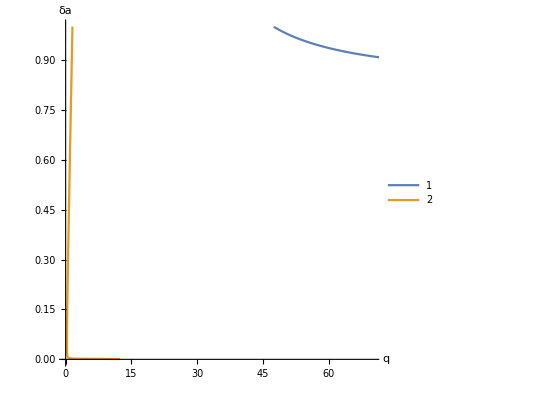

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δa"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}}
]
```

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δa"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,3},{0,1}}
]
```

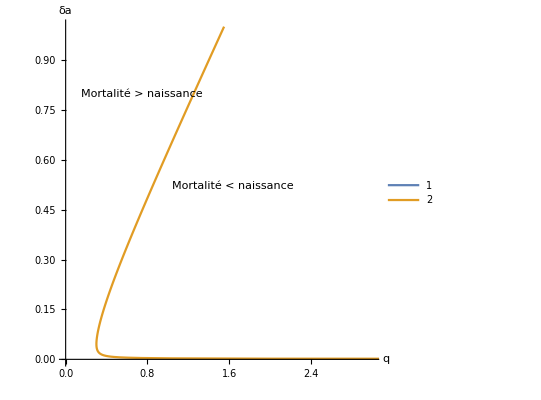

## Vérification avec des dynamique

### Paramètres

```mathematica
tmax=100;
τuN=4.72;τlN=16;τmN=8.92;αlN=0.001;δuN=0.0432;δlN=0.0048;δmN=0.0150;δjN=δuN; τjN=τuN;δpN=8;aN=1;qN=106.4;δaN=1/12.2;αlN=0.001;
```

```mathematica
UeqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN}
```

9.80944

```mathematica
AeqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN}
```

0.136038

```mathematica
PeqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN}
```

1.43096

```mathematica
HpEqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN}
```

0.000950957

```mathematica
Log[HpEqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN}]
```

-6.95804

### Zone de gauche

```mathematica
HpEqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->0.02,δa->0.06,δj->δjN,τj->τjN,δp->δpN,a->aN}
```

3.70326

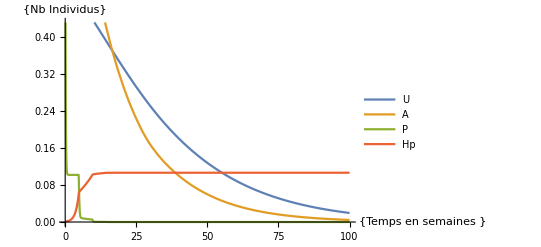

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->0.02,δa->0.06,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==0.0009509571743645905},{U,A,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],A[t],P[t],Hp[t]}/. solN],{t,0,tmax},PlotLegends->{"U","A","P","Hp"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

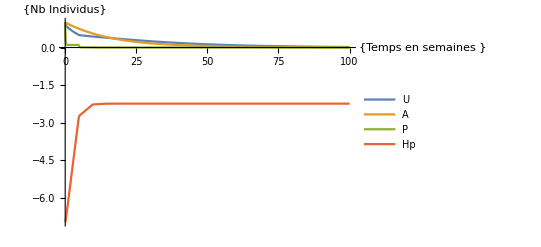

```mathematica
solN=NDSolve[{ModeleQuentin/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->0.02,δa->0.06,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==Log[0.0009509571743645905]},{U,A,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],A[t],P[t],Hp[t]}/. solN],{t,0,tmax},PlotLegends->{"U","A","P","Hp"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

### Zone de centre

```mathematica
HpEqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->30,δa->0.6,δj->δjN,τj->τjN,δp->δpN,a->aN}
```

0.0246884

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[(NDSolve`IndexReductionDump`eq$40361[#1]=#2)&,{{-5},{}}]; dimensions are 1 and 0.

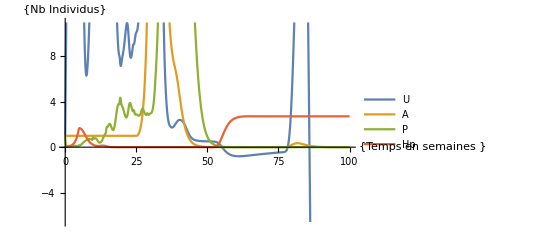

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->30,δa->0.6,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==0.024688369777983745},{U,L,A,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],A[t],P[t],Hp[t]}/. solN],{t,0,tmax},PlotLegends->{"U","A","P","Hp"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

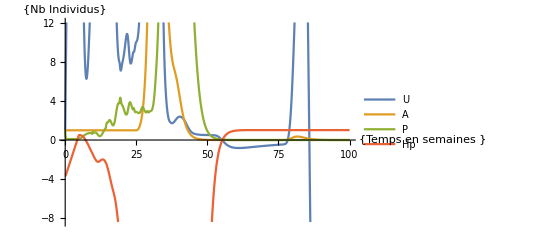

```mathematica
solN=NDSolve[{ModeleQuentin/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->30,δa->0.6,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==Log[0.024688369777983745]},{U,A,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->100000000000,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],A[t],P[t],Hp[t]}/. solN],{t,0,tmax},PlotLegends->{"U","A","P","Hp"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

### Zone de droite

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[(NDSolve`IndexReductionDump`eq$27184[#1]=#2)&,{{-5},{}}]; dimensions are 1 and 0.

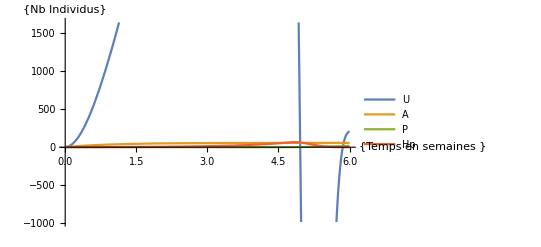

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->70,δa->1,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==1},{U,L,A,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4}];
Plot[Evaluate[{U[t],A[t],P[t],Hp[t]}/. solN],{t,0,tmax},PlotLegends->{"U","A","P","Hp"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

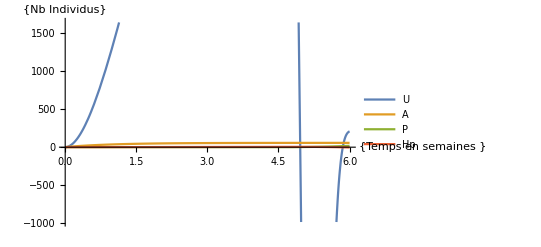

```mathematica
solN=NDSolve[{ModeleQuentin/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->70,δa->1,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1,Hp[t/;t<=0]==0},{U,A,P,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],A[t],P[t],Hp[t]}/. solN],{t,0,tmax},PlotLegends->{"U","A","P","Hp"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

## Comparaison de dynamique avec Julia

### Paramétrisation

### Recherche de valeur d’initialisation du FindRoot

### Création des Courbes

### Affichage des résultats

## Dynamiques

### Paramètres

```mathematica
tmax=3;
τuN=4.72;τlN=16;τmN=8.92;αlN=0.001;δuN=0.0432;δlN=0.0048;δmN=0.0150;δjN=δuN; τjN=τuN;δpN=8;aN=1;qN=106.4;δaN=1/12.2;αlN=0.001;
```

```mathematica
UeqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN}
```

9.80944

## Comparaison de dynamique avec Julia

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[(NDSolve`IndexReductionDump`eq$12153[#1]=#2)&,{{-5,-6},{}}]; dimensions are 2 and 0.

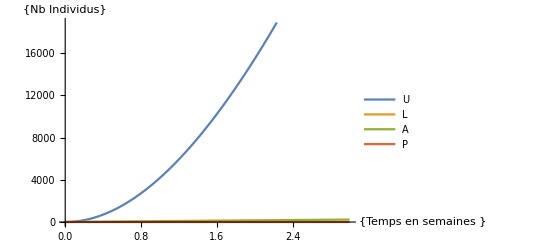

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1, Hc[t/;t<=0]==1,Hp[t/;t<=0]==1},{U,L,A,P,Hc,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],A[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","A","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

```mathematica
solN=NDSolve[{ModeleQuentin/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1, Hc[t/;t<=0]==0,Hp[t/;t<=0]==0},{U,L,A,P,Hc,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],A[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","A","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[(NDSolve`IndexReductionDump`eq$11612[#1]=#2)&,{{-5,-6},{}}]; dimensions are 2 and 0.

-Graphics-